http : // www.pitt.edu/~tabakin/QDENSITY

```mathematica
Needs["QDENSITY`Qdensity`","C:\\Qdensity.m"];
KetBra::usage="|x/(d - 1)⟩⟨y/(d - 1)| of ℂ^d, where x,y∈{0,...,d-1} and |0⟩,|1/(d - 1)⟩,...,|1⟩ are the elements of the canonical basis of ℂ^d";
KetBra[d_,x_,y_]:=SparseArray[{{x+1,y+1}->1},{d,d}];
BlochVector::usage="BlochVector[ρ], where ρ is a density operator of ℂ^d and d≥2.
\n\t Returns the corresponding Bloch vector b∈R^(d^2).";
BlochVector[ρ_]:=Block[{d,sigma},
d=Dimensions[ρ][[2]];
sigma={};
Do[AppendTo[sigma,KetBra[d,l,k]+KetBra[d,k,l]],{l,0,d-2},{k,l+1,d-1}];
Do[AppendTo[sigma,-ⅈ KetBra[d,k,l]+ⅈ KetBra[d,l,k]],{l,0,d-2},{k,l+1,d-1}];
Do[AppendTo[sigma,√(2/(l(l+1)))(Sum[ KetBra[d,k,k],{k,0,l-1}] -l KetBra[d,l,l])],{l,1,d-1}];
Tr[ρ.#]&/@sigma];
BlochVectorInverse::usage="BlochVectorInverse[b]
\n\t Returns the density operator of ℂ^d of the Bloch vector b∈R^(d^2).
\n\t Not any vector b of the unit hypershpere gives rise a density operator,
since the output is not a semi-definite positive operator (i.e. there exists a negative eigenvalue),
\n\t but all vectors of length ⩽2/d give rise a density operator.";
BlochVectorInverse[b_]:=Block[{d,sigma,ρ},
d=Ceiling[√(Length[b]+1)];
sigma={};
Do[AppendTo[sigma,KetBra[d,l,k]+KetBra[d,k,l]],{l,0,d-2},{k,l+1,d-1}];
Do[AppendTo[sigma,-ⅈ KetBra[d,k,l]+ⅈ KetBra[d,l,k]],{l,0,d-2},{k,l+1,d-1}];
Do[AppendTo[sigma,√(2/(l(l+1)))(Sum[ KetBra[d,k,k],{k,0,l-1}] -l KetBra[d,l,l])],{l,1,d-1}];
b=2/d PadRight[b,d];
 ρ=1/d IdentityMatrix[d]+√((d-1)/(2 d))Sum[b[[j]]sigma[[j]],{j,1,d^2-1}];
Return[ρ]];
SVMEncoder::usage="SVMEncoder[x,type], where x∈R^(d - 1) (keeps the value |x| and normalizes the new vector if type=1).
\n\t When type=2, it uses the inverse of the stereographic projection.
\n\t Returns the density operator of ℂ^d,
which is projection-operator (that projects over the closed subspace determined by the normalized vector) if type is 1 or 2.
\n\t It is a mixed state with the corresponding Bloch vector of length 2/d if type=3.";
SVMEncoder[x_,type_]:=Block[{u,ρ},
u=Switch[type,1,Normalize[Append[x,1]],2,2/(Total[x^2]+1)Append[x,1/2(Total[x^2]-1)],3,Normalize[Append[x,1]]];
If[type==3 ,ρ=BlochVectorInverse[u],ρ=Outer[Times,u,u]];Return[ρ]];
BinaryClassifier::usage="BinaryClassifier[DClass1,DClass2],
where DClass1 and DClass2 are density operators of the class 1 and 2, respectively. 
\n\t Returns the projection-operators P+ and P-.";
BinaryClassifier[DClass1_,DClass2_]:=Block[{p,c,vals,vecs,prjs,prj1,prj2},
p=Length[DClass1]/(Length[DClass1]+Length[DClass2]);
c=p Total[DClass1]-(1-p)Total[DClass2];{vals,vecs}=Eigensystem[c];
vecs=Normalize/@vecs;prjs=Outer[Times,Conjugate[#],#]&/@vecs;
prj1=Total[Pick[prjs,NonNegative[vals]]];
prj2=Total[Pick[prjs,Negative[vals]]];
Return[{prj1,prj2}]];
HelstromClassify::usage="HelstromClassify[{P+,P-},ρ].
\n\t Returns the class 1 or 2.";
HelstromClassify[{prj1_,prj2_},ρ_]:=If[Tr[prj1.#]≥Tr[prj2.#],1 ,2]&/@ρ;
ToDensity[B_]:=Block[{sigma,ρ},
sigma={KetBra[2,0,1]+KetBra[2,1,0],-ⅈ KetBra[2,1,0]+ⅈ KetBra[2,0,1],KetBra[2,0,0]- KetBra[2,1,1]};
ρ={};Do[AppendTo[ρ,1/2(IdentityMatrix[2]+Sum[B[[i,j]]sigma[[j]],{j,3}])],{i,Length[B]}];Return[ρ]];
unstandardize[point_,sd_,mu_]:=point*sd+mu;
getvectors[cf_ClassifierFunction,X_]:=With[{p=X},With[{sd=StandardDeviation[p],mu=Mean[p]},
unstandardize[#,sd,mu]&/@cf[[1]]["Model"]["TrainedModel"][[1]]["supportVectors"]]]
getplane[svmcf_ClassifierFunction,X_]:=With[{tm=svmcf[[1]]["Model"]["TrainedModel"][[1]],points=X},
Module[{sv=tm["supportVectors"],svc=tm["supportVectorCoefficients"],
sd=StandardDeviation[points],mu=Mean[points],dim=Length[points[[1]]],vecs,offset},
vecs=Rest[RotationMatrix[{svc.sv,PadRight[{1},dim]}].IdentityMatrix[dim]];
offset=With[{vars=Array[x,dim]},Values@First@FindInstance[vars.(svc.sv)==tm["rho"],vars]];
vecs=sd*#&/@vecs;
offset=unstandardize[offset,sd,mu];
If[dim>2,InfinitePlane[offset,vecs],InfiniteLine[offset,First[vecs]]]]]
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

```mathematica
FullSimplify[BlochVectorInverse[2/(x1^2+x2^2+1){x1,x2,(x1^2+x2^2-1)/2}]]
```

(1-1/(1+x1^2+x2^2) | (x1+ⅈ x2)/(1+x1^2+x2^2)
(x1-ⅈ x2)/(1+x1^2+x2^2) | 1/(1+x1^2+x2^2))

```mathematica
rhoX=({{(x1^2+x2^2)/(1+x1^2+x2^2), (x1-ⅈ x2)/(1+x1^2+x2^2)}, {(x1+ⅈ x2)/(1+x1^2+x2^2), 1/(1+x1^2+x2^2)}});rhoY=({{(y1^2+y2^2)/(1+y1^2+y2^2), (y1-ⅈ y2)/(1+y1^2+y2^2)}, {(y1+ⅈ y2)/(1+y1^2+y2^2), 1/(1+y1^2+y2^2)}});FullSimplify[1/2 Total[Abs[Eigenvalues[rhoX-rhoY]]]](*Trace distance*)
```

Abs[(√((x1-y1)^2+(x2-y2)^2))/(√(1+x1^2+x2^2) √(1+y1^2+y2^2))]

```mathematica
FullSimplify[2/(√(1-(x1^2+x2^2-1)/(x1^2+x2^2+1))√(1-(y1^2+y2^2-1)/(y1^2+y2^2+1)))(√((x1-y1)^2+(x2-y2)^2))/(√(1+x1^2+x2^2) √(1+y1^2+y2^2))]
```

√(1/(1+x1^2+x2^2)) √(1+x1^2+x2^2) √((x1-y1)^2+(x2-y2)^2) √(1/(1+y1^2+y2^2)) √(1+y1^2+y2^2)

DBSCAN with a toy dataset

ClassifierFunction[…]

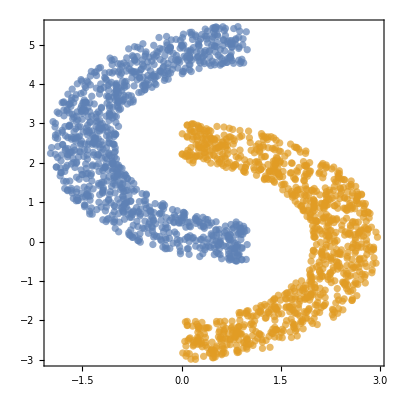

```mathematica
circle[r_,theta_]:={r Sin[theta],r Cos[theta]};
{train,test}=With[{rot=RotationTransform[π,{0,0}],tra=TranslationTransform[{1,2.5}],
pts=circle@@@RandomVariate[UniformDistribution[{{2,3},{0,Pi}}],2000]},
TakeDrop[RandomSample@Join[tra[rot[pts]],pts],2000]];
cl=ClusterClassify[train,Method->"DBSCAN"]
ListPlot[Pick[test,cl[test],#]&/@Range[2],PlotStyle->Directive[PointSize[0.013],Opacity[0.7]],
AspectRatio->1,Frame->True,Axes->False]
{X1,X2}=Pick[train,cl[train],#]&/@Range[2];
{X1Test,X2Test}=Pick[test,cl[test],#]&/@Range[2];
```

0.8455

-Graphics3D-

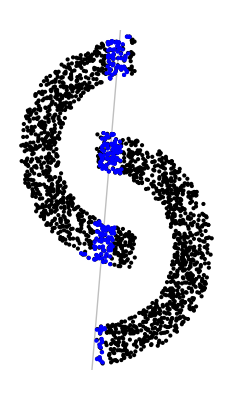

<|Linear→0.9475,RadialBasisFunction→0.9915,Polynomial→0.996,Sigmoid→0.889|>

0.8365

```mathematica
D1=SVMEncoder[#,1]&/@X1;
D2=SVMEncoder[#,1]&/@X2;
{p1,p2}=BinaryClassifier[D1,D2];
y1=HelstromClassify[{p1,p2},D1];
y2=HelstromClassify[{p1,p2},D2];
accuracy[y1_,y2_]:=N[(Count[y1,1]+Count[y2,2])/(Length[y1]+Length[y2])];
accuracy[y1,y2]
Show[Plot3D[{Tr[p1.SVMEncoder[{x1,x2},1]],Tr[p2.SVMEncoder[{x1,x2},1]]},{x1,-10,10},{x2,-10,10},
PlotStyle->{Green,Red},ViewPoint->{0,0,∞},Lighting->{{"Ambient",White}},Mesh->False],
Graphics3D[{RGBColor[0,1,0,.5],PointSize[0.013],Point[Append[#,1]&/@X1]}],
Graphics3D[{RGBColor[1,0,0,.5],PointSize[0.013],Point[Append[#,1]&/@X2]}]]
y=Join[y1,y2];
X=Join[X1,X2];
HelstromX1=Pick[X,y,1];
HelstromX2=Pick[X,y,2];
svm=Classify[X-> y,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
Graphics[{Point[X],Blue,PointSize[Large],Point[getvectors[svm,X]],Opacity[.5],Gray,getplane[svm,X]}]
AssociationMap[ ClassifierMeasurements[Classify[X-> y,Method->{"SupportVectorMachine","KernelType"-> #}],
<|1->HelstromX1,2->HelstromX2|>, "Accuracy"]&,{"Linear","RadialBasisFunction","Polynomial","Sigmoid"}]
D1Test=SVMEncoder[#,1]&/@X1Test;
D2Test=SVMEncoder[#,1]&/@X2Test;
y1=HelstromClassify[{p1,p2},D1Test];
y2=HelstromClassify[{p1,p2},D2Test];
accuracy[y1,y2]
```

0.503

-Graphics3D-

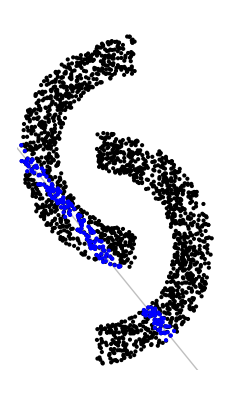

<|Linear→0.9925,RadialBasisFunction→0.9905,Polynomial→0.9955,Sigmoid→0.8655|>

```mathematica
D1C=ToDensity[Normalize[Append[#,1]]&/@X1];
D2C=ToDensity[Normalize[Append[#,1]]&/@X2];
{p1C,p2C}=BinaryClassifier[D1C,D2C];
y1=HelstromClassify[{p1C,p2C},D1C];
y2=HelstromClassify[{p1C,p2C},D2C];
accuracy[y1,y2]
Show[Plot3D[{Tr[p1C.ToDensity[{Normalize[{x1,x2,1}]}][[1]]],
Tr[p2C.ToDensity[{Normalize[{x1,x2,1}]}][[1]]]},{x1,-10,10},{x2,-10,10},
PlotStyle->{Green,Red},ViewPoint->{0,0,∞},Lighting->{{"Ambient",White}},Mesh->False],
Graphics3D[{RGBColor[0,1,0,.5],PointSize[0.013],Point[Append[#,1]&/@X1]}],
Graphics3D[{RGBColor[1,0,0,.5],PointSize[0.013],Point[Append[#,1]&/@X2]}]]
y=Join[y1,y2];
HelstromX1=Pick[X,y,1];
HelstromX2=Pick[X,y,2];
svm=Classify[X-> y,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
Graphics[{Point[X],Blue,PointSize[Large],Point[getvectors[svm,X]],Opacity[.5],Gray,getplane[svm,X]}]
AssociationMap[ ClassifierMeasurements[Classify[X-> y,Method->{"SupportVectorMachine","KernelType"-> #}],
<|1->HelstromX1,2->HelstromX2|>, "Accuracy"]&,{"Linear","RadialBasisFunction","Polynomial","Sigmoid"}]
```

```mathematica
CentroidClassify[{mean1_,mean2_},D_]:=
If[Tr[ConjugateTranspose[mean1-#].(mean1-#)]≤Tr[ConjugateTranspose[mean2-#].(mean2-#)],1 ,2]&/@D;
mean1=Mean[D1];
mean2=Mean[D2];
y1=CentroidClassify[{mean1,mean2},D1];
y2=CentroidClassify[{mean1,mean2},D2];
accuracy[y1,y2]
B1=BlochVector[#]&/@D1;
B2=BlochVector[#]&/@D2;
mean1=Mean[B1];
mean2=Mean[B2];
CentroidClassify[{mean1_,mean2_},B_,p_]:=If[Norm[mean1-#,p]≤Norm[mean2-#,p] ,1 ,2]&/@B;
y1=CentroidClassify[{mean1,mean2},B1,2];
y2=CentroidClassify[{mean1,mean2},B2,2];
accuracy[y1,y2]
```

0.865

0.865

Heltrom classifier gives the best average success probability (1/2+1/2(1/2 | ρ_1-ρ_2|_1), 
but it does not work with the same centroid (such as 1/2 I).

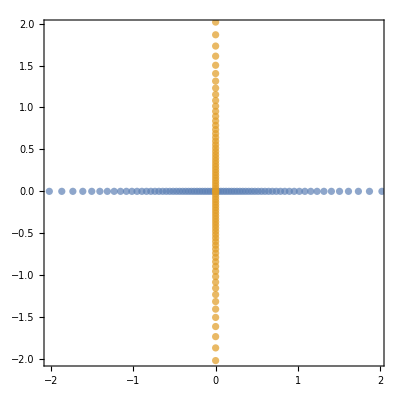

((0. | 0.
0. | 0.)
(0.82014 | 0.
0. | 0.17986)
(0.82014 | 0.
0. | 0.17986))

<|RandomForest→0.975,NaiveBayes→0.955,SupportVectorMachine→0.83,NearestNeighbors→0.985,LogisticRegression→0.5|>

```mathematica
X1=Table[{Tan[θ],0},{θ,0,2π,(2π)/99}];
X2=-RotateLeft[#,1]&/@X1;
ListPlot[{X1,X2},PlotStyle->Directive[PointSize[0.013],Opacity[0.7]],AspectRatio->1,Frame->True,Axes->False]
D1C=ToDensity[Normalize[Append[#,1]]&/@X1];
D2C=ToDensity[Normalize[Append[#,1]]&/@X2];
MatrixForm[#]&/@N[{Length[D1C]/(Length[D1C]+Length[D2C]) Total[D1C]-Length[D2C]/(Length[D1C]+Length[D2C])Total[D2C],Total[D1C]/Length[D1C],Total[D2C]/Length[D2C]}]
AssociationMap[ ClassifierMeasurements[Classify[<|1->X1,2->X2|>,Method->#],<|1->X1,2->X2|>, "Accuracy"]&,
{"RandomForest", "NaiveBayes", "SupportVectorMachine", "NearestNeighbors","LogisticRegression"}]
```

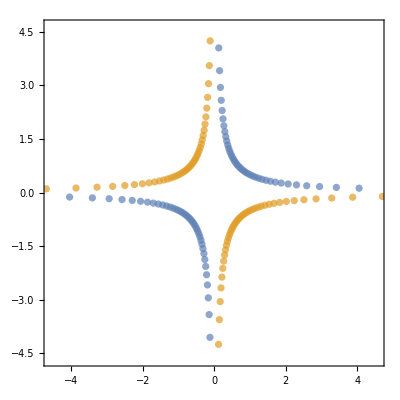

0.73

-Graphics3D-

((0.250031 | 12.5 | 0
12.5 | -0.250031 | 0
0 | 0 | 0)
(0.375 | 0.125 | 0
0.125 | 0.375 | 0
0 | 0 | 0.25)
(0.369999 | -0.125 | 0
-0.125 | 0.380001 | 0
0 | 0 | 0.25))

<|RandomForest→0.98,NaiveBayes→0.545,SupportVectorMachine→0.45,NearestNeighbors→0.85,LogisticRegression→0.5|>

```mathematica
X1=N[Flatten[Table[{{(Cot[θ]+Csc[θ])/(√2),Tan[θ/2]/(√2)},{-Cot[θ/2]/(√2),((-1+Cos[θ]) Csc[θ])/(√2)}},{θ,π/100,π-π/100,(2π)/100}],1]];
X2=N[Flatten[Table[{{Tan[θ/2]/(√2),-Cot[θ/2]/(√2)},{((-1+Cos[θ]) Csc[θ])/(√2),(Cot[θ]+Csc[θ])/(√2)}},{θ,π/200,π-π/200,(2π)/100}],1]];
ListPlot[{X1,X2},PlotStyle->Directive[PointSize[0.013],Opacity[0.7]],AspectRatio->1,Frame->True,Axes->False]
D1=SVMEncoder[#,1]&/@X1;
D2=SVMEncoder[#,1]&/@X2;
{p1,p2}=BinaryClassifier[D1,D2];
y1=HelstromClassify[{p1,p2},D1];
y2=HelstromClassify[{p1,p2},D2];
accuracy[y1,y2]
Show[Plot3D[{Tr[p1.SVMEncoder[{x1,x2},1]],Tr[p2.SVMEncoder[{x1,x2},1]]},{x1,-10,10},{x2,-10,10},
PlotStyle->{Green,Red},ViewPoint->{0,0,∞},Lighting->{{"Ambient",White}},Mesh->False],
Graphics3D[{RGBColor[0,1,0,.5],PointSize[0.013],Point[Append[#,1]&/@X1]}],
Graphics3D[{RGBColor[1,0,0,.5],PointSize[0.013],Point[Append[#,1]&/@X2]}]]
MatrixForm[#]&/@Chop[N[{Length[D1]/(Length[D1]+Length[D2]) Total[D1]-Length[D2]/(Length[D1]+Length[D2])Total[D2],Total[D1]/Length[D1],Total[D2]/Length[D2]}]]
AssociationMap[ ClassifierMeasurements[Classify[<|1->X1,2->X2|>,Method->#],<|1->X1,2->X2|>, "Accuracy"]&,
{"RandomForest", "NaiveBayes", "SupportVectorMachine", "NearestNeighbors","LogisticRegression"}]
```

```mathematica
FeatureVector::usage="FeatureVector[m,n,type],
where m is the dimension of the input vector, n is the number of copies of the density operator, type of the SVMEncoder
\n\t Returns the feature vector.";
FeatureVector[m_,n_,type_]:= Block[{ρ,state,x},
ρ=SVMEncoder[Array[x,m],type];
state=Nest[TensorProductQD[ρ,#]&,ρ,n-1];
DeleteDuplicates[DeleteCases[BlochVector[state],0]]];
FeatureVector[2,1,2]
```

((8 x[1] x[2])/((1+x[1]^2+x[2]^2)^2)
(4 x[1] (-1+x[1]^2+x[2]^2))/((1+x[1]^2+x[2]^2)^2)
(4 x[2] (-1+x[1]^2+x[2]^2))/((1+x[1]^2+x[2]^2)^2)
(4 x[1]^2)/((1+x[1]^2+x[2]^2)^2)-(4 x[2]^2)/((1+x[1]^2+x[2]^2)^2)
(4 x[1]^2)/(√3 (1+x[1]^2+x[2]^2)^2)+(4 x[2]^2)/(√3 (1+x[1]^2+x[2]^2)^2)-(2 (-1+x[1]^2+x[2]^2)^2)/(√3 (1+x[1]^2+x[2]^2)^2))

```mathematica
SVMEncoder[2/(1+x1^2+x2^2){x1,x2,(-1+x1^2+x2^2)/2},3]//MatrixForm
```